```mathematica
(*Да,программа короткая-используется пара-тройка формул.Во-первых,последовательными итерациями решается уравнение для нахождения запаздывающего момента времени $t'$:$$c(t-t')=r(t')$$.
Здесь $r(t')=\sqrt{(x-s(t'))^2+y^2}$-расстояние от заряда до точки наблюдения $(x,\,y)$ в момент $t'$,а $s(t)$-текущая координата заряда.Во-вторых,сама формула для потенциала
$$\varphi(x,\,y,\,t)=\frac{q}{r(t')-\vec{v}(t')\cdot\vec{r}(t')/c}$$
или
$$\varphi(x,\,y,\,t)=\frac{q}{c(t-t')-v(t')(x-s(t'))/c}$$,где $v(t)=ds(t)/dt$-скорость заряда.*)
v=0.84; (* скорость *)
c = 1.0;
```

```mathematica
s[t_]:=v*t;(*координата от времени*)
```

```mathematica
tzap[x_,y_,t_]:=Module[{tz},tz=(t-x*v/c^2-Sqrt[(x-s[t])^2+(1-v^2/c^2)*(y^2)]/c)/(1-v^2/c^2);tz];
```

```mathematica
ss=
Table[Show[ContourPlot[tzap[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.08,0.36,0.02}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]], {t,0,30,0.25}];
Export["D://lienar-wiechert_v_const_t_zap_po_fejnmanu_tzap.gif",ss]
```

D://lienar-wiechert_v_const_t_zap_po_fejnmanu_tzap.gif

```mathematica
"D://lienar-wiechert_v_const_t_zap_po_fejnmanu.gif"
```

D://lienar-wiechert_v_const_t_zap_po_fejnmanu.gif

```mathematica
t=7.5;
```

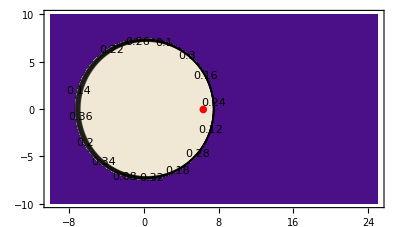

```mathematica
Show[ContourPlot[tzap[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.08,0.36,0.02}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]]
```

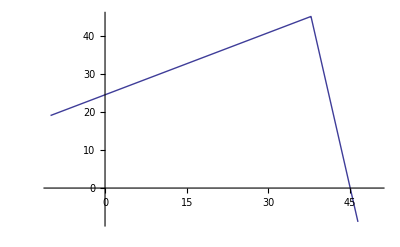

```mathematica
t=45;Plot[tzap[x,0,t],{x,-10,50}]
```

```mathematica
t=45;Value[tzap[x,0,t],{x,-10,50}]
```

Value[40.7609,{30,-10,50}]

```mathematica
x =30;phi[x,0,t]
```

0.128205